```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts2\\"];
```

```mathematica
(* script to check results from R *)
```

```mathematica
ClearAll[cd,gd];
gd[x_]=Assuming[x>0,FS[PDF[GammaDistribution[1,1000],x]]];

cd[x_]=Assuming[x>0,FS@Log[PDF[CauchyDistribution[Log[1000],Log[1000]],Log[x]]]]
```

Log[Log[1000]]-Log[π (18 Log[10]^2-6 Log[10] Log[x]+Log[x]^2)]

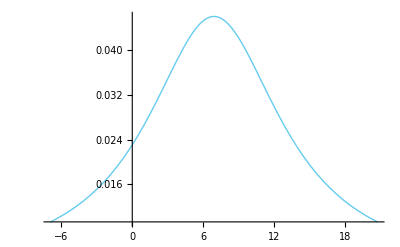

```mathematica
Plot[Exp[cd[lx]],{lx,Log[10^-3],Log[10^9]},PlotRange->Auto]
```

```mathematica
(* PAIR CHECKS *)
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
```

```mathematica
allcouples=Flatten[Table[{ii,jj},{ii,93},{jj,ii+1,94}],1];
```

```mathematica
allcouples[[1071]]
```

{13,34}

```mathematica
symptoms={{1}};snps={3+{5,83}};
symptomvariants={{0},{1}};snpvariants={{0,0},{0,1},{1,0},{1,1}};
namesymptomvariants={"n","y"};
namesymptoms="";namesnps="";namesnpvariants="";
```

```mathematica
{numsymptoms=Length[symptoms],numsymptomvariants=Length[symptomvariants],numsnps=Length[snps],numsnpvariants=Length[snpvariants],namestatistics=Flatten@Table[ii<>jj,{ii,{"EV_","SD_","post.theta_","opt.theta_","max.spread_"}},{jj,namesymptomvariants}]}
```

{1,2,1,4,{EV_n,EV_y,SD_n,SD_y,post.theta_n,post.theta_y,opt.theta_n,opt.theta_y,max.spread_n,max.spread_y}}

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=Total@cd[Log@t]-Total@Log[t];
```

```mathematica
<<conditional_freqs_1.m
```

```mathematica
spread=defaultspread;
```

```mathematica
(condc=condfreqstatistics[data,symptoms,symptomvariants,snps,snpvariants,namesymptoms,namesymptomvariants,namesnps,namesnpvariants,savedir,filename,logpriortheta,spread])//MF
```

((0.728532 | 0.415608 | 0.566438 | 0.707934
0.271468 | 0.584392 | 0.433562 | 0.292066
0.00638856 | 0.225994 | 0.255723 | 0.0131828
0.00638856 | 0.225994 | 0.255723 | 0.0131828
3529.56 | 1.5608 | 1.5608 | 841.561
1315.19 | 2.19466 | 1.19466 | 347.195
1.5608 | Null | Null | Null
1.19466 | Null | Null | Null
1.40608 | Null | Null | Null
1.40608 | Null | Null | Null))

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=gd[Total@t]-Log[Total@t];
```

```mathematica
<<conditional_freqs_1.m
```

```mathematica
spread=defaultspread;
```

```mathematica
(condg=condfreqstatistics[data,symptoms,symptomvariants,snps,snpvariants,namesymptoms,namesymptomvariants,namesnps,namesnpvariants,savedir,filename,logpriortheta,spread])//MF
```

((0.728555 | 0.360064 | 0.550927 | 0.708013
0.271445 | 0.639936 | 0.449073 | 0.291987
0.00638896 | 0.243489 | 0.292765 | 0.0131866
0.00638896 | 0.243489 | 0.292765 | 0.0131866
3529.04 | 1.03932 | 1.03932 | 841.039
1314.85 | 1.84718 | 0.847176 | 346.847
1.03932 | Null | Null | Null
0.847176 | Null | Null | Null
1.51286 | Null | Null | Null
1.51286 | Null | Null | Null))

```mathematica
condg[[1,1,5;;6,1]]
```

{3529.04,1314.85}

```mathematica
bd[x_,a_,b_]=PDF[BetaDistribution[b,a],x];
```

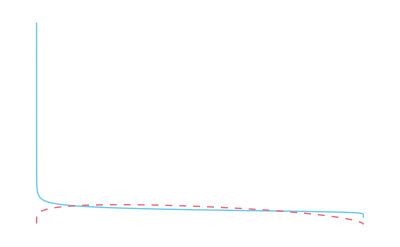

```mathematica
ss=3;Plot[{bd[x,Sequence@@condg[[1,1,5;;6,ss]]],bd[x,Sequence@@condc[[1,1,5;;6,ss]]]},{x,0,1},PlotRange->All]
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
```

```mathematica
symptoms={{1}};
snps={3+{5,83}};
symptomvariants={{0},{1}};snpvariants={{0,0},{0,1},{1,0},{1,1}};
namesymptomvariants={"n","y"};
namesymptoms="";
```

```mathematica
numsymptoms=Length[symptoms];numsymptomvariants=Length[symptomvariants];numsnps=Length[snps];numsnpvariants=Length[snpvariants];namestatistics=Flatten@Table[ii<>jj,{ii,{"EV_","SD_","post.theta_","opt.theta_","max.spread_"}},{jj,namesymptomvariants}];
```

```mathematica
sdata=data[[;;,Join[symptoms[[1]],snps[[1]]]]];
```

```mathematica
(f=Table[Total[Boole/@Table[z==Join[symptomvariant,snpvariant],{z,sdata}]],{symptomvariant,symptomvariants},{snpvariant,snpvariants}])//MF
```

(3528 | 0 | 0 | 840
1314 | 1 | 0 | 346)

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=(Log@gd[Total@t]-Log[Total@t]);
```

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=(Total@cd[t]-Total@Log[t]);
```

```mathematica
logprob[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+logpriortheta[t]];
```

```mathematica
theta=FindArgMax[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{8.49735,3.43841}

```mathematica
theta=FindArgMax[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{0.123298,0.101888}

```mathematica
FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{-3559.62,{t[1]→0.123298,t[2]→0.101888}}

```mathematica
logprob[t_]:=Block[{r2=f+t},Total@Flatten@LogGamma[r2]-Total@LogGamma[Total@r2]+numsnpvariants*(LogGamma[Total@t]-Total@LogGamma[t])+Total[logpriortheta[t]]];
```

```mathematica
f+{10^4,2*10^4}
```

{{11481,12887},{20502,21159}}

```mathematica
logprob[{1,2}]//N
```

-3568.75

```mathematica
thetas=Array[t,numsymptomvariants]
```

{t[1],t[2]}

```mathematica
thetas=Table[Unique["t"],numsymptomvariants]
```

{t45,t46}

```mathematica
FindArgMax[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{4.58319×10^-8,4.58319×10^-8}

```mathematica
FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]]
```

{-3565.28,{t45→41.0502,t46→16.3425}}

```mathematica
test[[2]]
```

{t45→41.0502,t46→16.3425}

```mathematica
theta=thetas/.FindMaximum[{logprob[thetas],Sequence@@((#>0)&/@thetas)},T[{thetas,Mean@T@f}]][[2]]
```

{{t39,t40}/.{t39,1092},{t39,t40}/.{t40,1661/4}}

```mathematica
fnew=f+theta
```

{{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343}}

```mathematica
nnew=Total[fnew]
```

{2028.39,2623.39,784.393,822.393}

```mathematica
Sequence@@T[T[fnew]/nnew]
```

Sequence[{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032}]

```mathematica
Sqrt[(Times@@fnew)/(nnew^2*(1+nnew))]
```

{0.00976638,0.00868929,0.0164497,0.01583}

```mathematica
Sqrt@T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]
```

{{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583}}

```mathematica
Table[Null,numsnpvariants-1,numsymptomvariants]
```

{{Null,Null},{Null,Null},{Null,Null}}

```mathematica
T@Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]
```

{{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
quantities={(*EV*)Sequence@@T[T[fnew]/nnew],(*STD*)Sequence@@Sqrt[T[((nnew-T@fnew)*T@fnew)/(nnew^2*(1+nnew))]],(*(*Quantiles*)Sequence@@(T@Table[Quantile[BetaDistribution[Sequence@@(Reverse[fnew[[;;,al]]])],quantiles],{al,binoutcomes+1}]),*)(*f+theta*)Sequence@@fnew,(*posterior theta*)Sequence@@T[Join[{theta},Table[Null,numsnpvariants-1,numsymptomvariants]]]}
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null}}

```mathematica
spread[q_]:=Max/@Abs@ArrayReshape[Table[(q[[co,x]]-q[[co,y]])/(q[[co+numsymptomvariants,x]]+q[[co+numsymptomvariants,y]]),{co,numsymptomvariants},{x,numsnpvariants-1},{y,x+1,numsnpvariants}],{numsymptomvariants,Binomial[numsnpvariants,2]}]
```

```mathematica
spread[quantities]
```

{1.67685,1.67685}

```mathematica
Join[quantities,T[Join[{spread[quantities]},Table[Null,numsnpvariants-1,numsymptomvariants]]]]
```

{{0.737555,0.727703,0.693594,0.708968},{0.262445,0.272297,0.306406,0.291032},{0.00976638,0.00868929,0.0164497,0.01583},{0.00976638,0.00868929,0.0164497,0.01583},{1496.05,1909.05,544.05,583.05},{532.343,714.343,240.343,239.343},{41.0502,Null,Null,Null},{16.3425,Null,Null,Null},{1.67685,Null,Null,Null},{1.67685,Null,Null,Null}}

```mathematica
(* TRIPLET CHECK *)
```

```mathematica
data=Import["dataset1_binarized.csv"][[2;;,2;;]];
```

```mathematica
symptoms={{2}};snps={{9,17,58}}+3;
symptomvariants={{0},{1}};

binvalues={0,1,2,4,3,5,6,7};
snpvariants=Reverse[IntegerDigits[#,2,3]]&/@binvalues;

namesymptomvariants={"n","y"};
namesymptoms="";namesnps="";namesnpvariants="";
```

```mathematica
{numsymptoms=Length[symptoms],numsymptomvariants=Length[symptomvariants],numsnps=Length[snps],numsnpvariants=Length[snpvariants],namestatistics=Flatten@Table[ii<>jj,{ii,{"EV_","SD_","post.theta_","opt.theta_","max.spread_"}},{jj,namesymptomvariants}]}
```

{1,2,1,8,{EV_n,EV_y,SD_n,SD_y,post.theta_n,post.theta_y,opt.theta_n,opt.theta_y,max.spread_n,max.spread_y}}

```mathematica
ClearAll[logpriortheta];logpriortheta[t_]:=gd[Total@t]-Log[Total@t];
```

```mathematica
<<conditional_freqs_1.m
```

```mathematica
spread=defaultspread;
```

```mathematica
T[Join[{namestatistics},T@#]&@condfreqstatistics[data,symptoms,symptomvariants,snps,snpvariants,namesymptoms,namesymptomvariants,namesnps,namesnpvariants,savedir,filename,logpriortheta,spread][[1,1]]]//MF
```

(EV_n | 0.566122 | 0.571833 | 0.601947 | 0.59387 | 0.559821 | 0.560503 | 0.653034 | 0.44868
EV_y | 0.433878 | 0.428167 | 0.398053 | 0.40613 | 0.440179 | 0.439497 | 0.346966 | 0.55132
SD_n | 0.00980377 | 0.0250689 | 0.0123554 | 0.0163197 | 0.0324795 | 0.0396626 | 0.0212115 | 0.0454797
SD_y | 0.00980377 | 0.0250689 | 0.0123554 | 0.0163197 | 0.0324795 | 0.0396626 | 0.0212115 | 0.0454797
post.theta_n | 1446.21 | 222.21 | 944.21 | 537.21 | 130.21 | 87.2103 | 328.21 | 53.2103
post.theta_y | 1108.38 | 166.383 | 624.383 | 367.383 | 102.383 | 68.3826 | 174.383 | 65.3826
opt.theta_n | 28.2103 | Null | Null | Null | Null | Null | Null | Null
opt.theta_y | 21.3826 | Null | Null | Null | Null | Null | Null | Null
max.spread_n | 4.07218 | Null | Null | Null | Null | Null | Null | Null
max.spread_y | 4.07218 | Null | Null | Null | Null | Null | Null | Null)

```mathematica
(* distribution of cond-frequency difference *)
```

```mathematica
bd[x_,a_,b_]=Assuming[a>0&&b>0,FS@PDF[BetaDistribution[a,b],x]]
```

Piecewise[{{((1-x)^(-1+b) x^(-1+a))/Beta[a,b], 0<x<1}, {0, True}}]

```mathematica
nd[x_,m_,v_]=PDF[NormalDistribution[m,v],x];
```

```mathematica
ev[a_]:=Mean[BetaDistribution[Sequence@@a]];
sd[a_]:=Sqrt@Variance[BetaDistribution[Sequence@@a]];
```

```mathematica
ClearAll[ol];ol[d_,a1_,a2_]:=NIntegrate[bd[x,Sequence@@a1]*bd[x-d,Sequence@@a2],{x,0,1}]
```

```mathematica
s1={505.437324355735,1489.4944182798};
s2={1162.43732435573,2895.4944182798};
```

```mathematica
evd=ev[s1]-ev[s2]
```

-0.0330998

```mathematica
sdd=Sqrt[sd[s1]^2+sd[s2]^2]
```

0.0120472

```mathematica
evd/sdd
```

-2.74751

```mathematica
NIntegrate[ol[d,s1,s2],{d,-0.01,0.01}]
```

0.0279721

```mathematica
Integrate[nd[d,evd,sdd],{d,-0.01,0.01}]
```

0.0274176

```mathematica
Integrate[nd[d,evd,sdd],{d,-0.05,0.05}]
```

0.919666

```mathematica
Plot[ol[d,1481,502,2887,1159],{d,-1,1}]
```

$Aborted

```mathematica
ol[0.1,s1,s2]
```

4.98572×10^-24

```mathematica
data=Table[{d,ol[d,s1,s2]},{d,evd-5*sdd,evd+5*sdd,sdd/5}];
```

```mathematica
datan=Table[{d,nd[d,evd,sdd]},{d,evd-5*sdd,evd+5*sdd,sdd/5}];
```

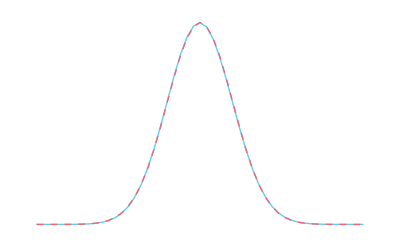

```mathematica
ListPlot[{data,datan},Joined->True,PlotRange->{All,{0,All}}]
```

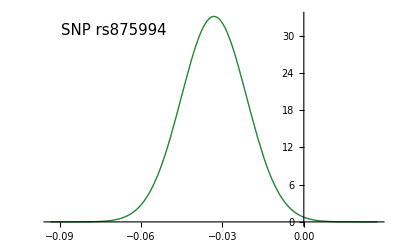

```mathematica
plot=Plot[nd[d,evd,sdd],{d,evd-5*sdd,evd+5*sdd},PlotRange->{0,All},Axes->{False,True},PlotStyle->{Thick,green},FrameLabel->{Subscript[f,HoldForm["O |"a]]-Subscript[f,HoldForm["O |"b]],"p"[HoldForm[Subscript[f,"O |"a]-Subscript[f,"O |"b]"| data"]]},Epilog->Text[Style["SNP rs875994",15],Sequence@@textposition[{0.05,0.95}]]]
```

```mathematica
Export["difference_symA_snp6.pdf",%,ImageSize->a5rsize]
```

difference_symA_snp6.pdf

```mathematica
Export["difference_symA_snp6.png",plot,ImageSize->a5rsize]
```

difference_symA_snp6.png

```mathematica
bd[0.2,Sequence@@s1]
```

2.66547280005×10^-6

```mathematica
Plot3D[bd[x,Sequence@@s1]*bd[y,Sequence@@s2],{x,ev[s1]-5*sd[s1],ev[s1]+5*sd[s1]},{y,ev[s2]-5*sd[s2],ev[s2]+5*sd[s2]},PlotRange->All,Axes->Auto]
```

-Graphics3D-

```mathematica
plot=Plot3D[bd[x,Sequence@@s1]*bd[y,Sequence@@s2],{x,0,1},{y,0,1},PlotRange->All,Axes->Auto,ViewPoint->Dynamic[viewpoint],Ticks->{Auto,Auto,None},Axes->Auto,AxesLabel->{Subscript[f,HoldForm[O"|"a]],Subscript[f,HoldForm[O"|"b]],Rotate["p"[HoldForm[Subscript[f,"O |"a]","Subscript[f,O"|"b]"| "D", initial info" ]],Pi/2,{1.7,0}]}]
```

-Graphics3D-

```mathematica
Export["testpostf.png",plot,ImageSize->a5rsize*1.25];
```

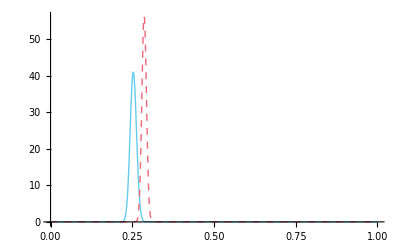

```mathematica
Plot[{bd[x,Sequence@@s1],bd[x,Sequence@@s2]},{x,0,1},PlotRange->All]
```

```mathematica
bd[x_,a_,b_]=Assuming[a>0&&b>0,FS@PDF[BetaDistribution[a,b],x]]
```

Piecewise[{{((1-x)^(-1+b) x^(-1+a))/Beta[a,b], 0<x<1}, {0, True}}]

```mathematica
nd[x_,m_,v_]=PDF[NormalDistribution[m,v],x];
```

```mathematica
ev[a_]:=Mean[BetaDistribution[Sequence@@a]];
sd[a_]:=Sqrt@Variance[BetaDistribution[Sequence@@a]];
```

```mathematica
ClearAll[ol];ol[d_,a1_,a2_]:=NIntegrate[bd[x,Sequence@@a1]*bd[x-d,Sequence@@a2],{x,0,1}]
```

```mathematica
s1={565.936085995177,1487.18448424005};
s2={1104.93608599518,2905.18448424005};
```

```mathematica
evd=ev[s1]-ev[s2]
```

0.000109912

```mathematica
sdd=Sqrt[sd[s1]^2+sd[s2]^2]
```

0.012123

```mathematica
evd/sdd
```

0.00906636

```mathematica
ol[0.1,s1,s2]
```

2.36883×10^-13

```mathematica
data=Table[{d,ol[d,s1,s2]},{d,evd-5*sdd,evd+5*sdd,sdd/5}];
```

```mathematica
datan=Table[{d,nd[d,evd,sdd]},{d,evd-5*sdd,evd+5*sdd,sdd/5}];
```

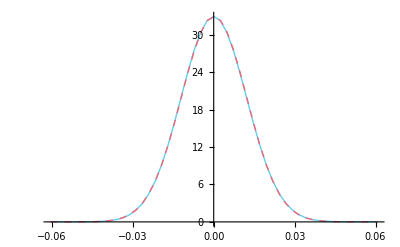

```mathematica
ListPlot[{data,datan},Joined->True,PlotRange->{All,{0,All}},Axes->{False,True}]
```

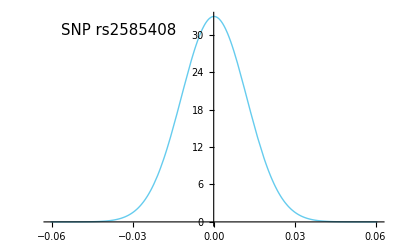

```mathematica
Plot[nd[d,evd,sdd],{d,evd-5*sdd,evd+5*sdd},PlotRange->{0,All},Axes->{False,True},FrameLabel->{Subscript[f,HoldForm[S"|"a]]-Subscript[f,HoldForm[S"|"b]],"p"[HoldForm[Subscript[f,S"|"a]-Subscript[f,S"|"b]"| data"]]},Epilog->Text[Style["SNP rs2585408",15],Sequence@@textposition[{0.05,0.95}]]]
```

```mathematica
Export["difference_symA_snp68.pdf",%,ImageSize->a5rsize]
```

difference_symA_snp68.pdf

```mathematica
Plot[{bd[x,Sequence@@s1],bd[x,Sequence@@s2]},{x,0,1},PlotRange->All]
```

-Graphics-